## Import Utils

```mathematica
Get["D:\\Documents\\workspace\\课题\\workspace\\Local\\Public\\mathematica\\PN_inverse\\InversePNUtils.nb"];
```

```mathematica
(*NotebookEvaluate["D:\\Documents\\workspace\\课题\\PN_inverse\\InversePNUtils.nb"]*)
```

```mathematica
NotebookEvaluate["D:\\Documents\\workspace\\课题\\workspace\\Local\\Public\\mathematica\\PN_inverse\\InversePNUtils.nb"];
```

输入Mc范围：{8,15}

输入q范围：{1,20}

m1范围：{9.18959,91.4002}

m2范围：{2.43734,17.2305}

输入Mc范围：{6,13}

输入q范围：{1,7}

m1范围：{6.89219,42.9142}

m2范围：{2.8295,14.9331}

全局极小值结果：{0.,{m1→3.,m2→3.,spin1z→0.99,spin2z→0.99}}

全局极大值结果：{0.,{m1→3.,m2→3.,spin1z→0.99,spin2z→0.99}}

全局极小值结果：{2.81559×10^-11,{m1→46.8969,m2→60.4341,spin1z→0.435746,spin2z→-0.638885}}

全局极大值结果：{8.65708,{m1→100.,m2→3.,spin1z→0.99,spin2z→0.99}}

全局极小值结果：{8.47209×10^-10,{m1→60.1419,m2→76.87,spin1z→0.320417,spin2z→-0.443897}}

全局极大值结果：{1.94773,{m1→100.,m2→3.,spin1z→0.99,spin2z→0.99}}

### Read from CSV

```mathematica
(* ==================配置==================*)
baseDir="D:\\Documents\\workspace\\课题\\workspace\\Local\\Parameterized_PN_Tests\\csv";
eventID="GW150914";

(*键名直接用短名，里面加上下划线*)
inspiralParams={"dphi_0","dphi_2","dphi_3","dphi_4","dphi_5l","dphi_6","dphi_6l","dphi_7"};
intermediateParams={"dbeta_2","dbeta_3"};
mergerParams={"dalpha_2","dalpha_3","dalpha_4"};

allParams=Join[inspiralParams,intermediateParams,mergerParams];

(* ==================读取函数==================*)
readDeviationFile[shortName_]:=Module[{path,raw},(*短名拼接上 _IMRP_posterior 还原成完整文件名*)path=FileNameJoin[{baseDir,eventID,shortName<>"_IMRP_posterior.csv"}];
raw=Import[path];
(*提取前五列*){raw[[2;;,1]],(*m1*)raw[[2;;,2]],(*m2*)raw[[2;;,3]],(*spin1z*)raw[[2;;,4]],(*spin2z*)raw[[2;;,5]]  (*偏差参数值*)}]

(*批量读取，键名就是传入的 shortName*)
readAllDeviations[]:=AssociationMap[readDeviationFile,allParams]

(* ==================执行==================*)
samples=readAllDeviations[];

(* ==================用法示例==================*)
(*直接用短名取值*)
dphi0vals=samples["dphi_0"][[5]];
dalpha3vals=samples["dalpha_3"][[5]];
```

```mathematica
raw=Import[FileNameJoin[{baseDir,eventID,"GR"<>"_IMRP_posterior.csv"}]];
samples["GR"]=(*提取前五列*){raw[[2;;,1]],(*m1*)raw[[2;;,2]],(*m2*)raw[[2;;,3]],(*spin1z*)raw[[2;;,4]](*spin2z*)};
```

```mathematica
Quantile[samples["GR"][[1]],{0.05,0.50,0.95}]
Quantile[samples["GR"][[2]],{0.05,0.50,0.95}]
Quantile[samples["GR"][[2]],{0.05,0.50,0.95}]
```

{32.4086,35.2935,40.2245}

{25.9935,30.3388,33.2104}

{25.9935,30.3388,33.2104}

## Calculate GR pars and further Transform $\delta$ into parameterized pars

```mathematica
(*批量计算非自旋 GR 系数值*)getGRValues[paramName_,m1s_,m2s_,chi1Ls_,chi2Ls_]:=Module[{etas},etas=etaFromMasses[m1s,m2s];
Switch[paramName,
(* =====Alpha (并合段)=====*)
"dalpha_2",IMRPhenomDAlpha[2,m1s,m2s,chi1Ls,chi2Ls],
"dalpha_3",IMRPhenomDAlpha[3,m1s,m2s,chi1Ls,chi2Ls],
"dalpha_4",IMRPhenomDAlpha[4,m1s,m2s,chi1Ls,chi2Ls],
(* =====Beta (过渡段)=====*)
"dbeta_2",IMRPhenomDBeta[2,m1s,m2s,chi1Ls,chi2Ls],
"dbeta_3",IMRPhenomDBeta[3,m1s,m2s,chi1Ls,chi2Ls],
(* =====Phi (旋近段)=====因为设置了 Listable，直接把整个 m1s,m2s 列表传进去即可，内部会自动对每个元素计算并返回列表*)
"dphi_0",IMRPhenomDPhiNS[0,m1s,m2s,0,0],
"dphi_2",IMRPhenomDPhiNS[2,m1s,m2s,0,0],
"dphi_3",IMRPhenomDPhiNS[3,m1s,m2s,0,0],
"dphi_4",IMRPhenomDPhiNS[4,m1s,m2s,0,0],
"dphi_5l",IMRPhenomDPhiLNS[5,m1s,m2s,0,0],
"dphi_6",IMRPhenomDPhiNS[6,m1s,m2s,0,0],
"dphi_6l",IMRPhenomDPhiLNS[6,m1s,m2s,0,0],
"dphi_7",IMRPhenomDPhiNS[7,m1s,m2s,0,0],
_,ConstantArray[0,Length[m1s]]
]
];

(* ==========对所有参数追加第6列(GR值)和第7列(参数化值)==========*)
Do[Module[{grVals,paramVals},
(*第6列：非自旋 GR 系数值*)grVals=getGRValues[p,samples[p][[1]],samples[p][[2]],samples[p][[3]],samples[p][[4]]];
(*第7列：参数化值=GR×(1+d)*)paramVals=grVals*(1+samples[p][[5]]);
(*拼接到原来的5列后面*)samples[p]=Join[samples[p],{grVals,paramVals}];
],{p,allParams}];
```

```mathematica
samples["dalpha_3"][[6]]
```

```mathematica
CalculateSampleRatios[samples,{35.5,29.9},{35.5-3.1,29.9-4.5},{35.5+5.1,29.9+3.0}]
```

{<|p→dphi_0,LowerBoundRatios→<|1→1.05627,2→0.841538|>,MedianRatios→<|1→1.0885,2→0.994134|>,UpperBoundRatios→<|1→1.09104,2→1.06441|>,WidthRatios→<|1→1.22842,2→1.81918|>|>,<|p→dphi_2,LowerBoundRatios→<|1→1.04185,2→0.827033|>,MedianRatios→<|1→1.09698,2→0.958047|>,UpperBoundRatios→<|1→1.09844,2→1.04686|>,WidthRatios→<|1→1.32205,2→1.79133|>|>,<|p→dphi_3,LowerBoundRatios→<|1→1.03444,2→0.844279|>,MedianRatios→<|1→1.07575,2→0.982997|>,UpperBoundRatios→<|1→1.08597,2→1.04639|>,WidthRatios→<|1→1.28956,2→1.73087|>|>,<|p→dphi_4,LowerBoundRatios→<|1→1.04008,2→0.822671|>,MedianRatios→<|1→1.10338,2→0.951138|>,UpperBoundRatios→<|1→1.10638,2→1.04022|>,WidthRatios→<|1→1.36831,2→1.77698|>|>,<|p→dphi_5l,LowerBoundRatios→<|1→1.04654,2→0.846059|>,MedianRatios→<|1→1.09595,2→0.96028|>,UpperBoundRatios→<|1→1.0979,2→1.035|>,WidthRatios→<|1→1.30082,2→1.6749|>|>,<|p→dphi_6,LowerBoundRatios→<|1→1.04267,2→0.901142|>,MedianRatios→<|1→1.07958,2→0.987286|>,UpperBoundRatios→<|1→1.08485,2→1.04476|>,WidthRatios→<|1→1.25151,2→1.53115|>|>,<|p→dphi_6l,LowerBoundRatios→<|1→1.03872,2→0.868742|>,MedianRatios→<|1→1.08513,2→0.977471|>,UpperBoundRatios→<|1→1.07935,2→1.04093|>,WidthRatios→<|1→1.23988,2→1.62406|>|>,<|p→dphi_7,LowerBoundRatios→<|1→1.04554,2→0.918951|>,MedianRatios→<|1→1.075,2→0.993093|>,UpperBoundRatios→<|1→1.08226,2→1.04587|>,WidthRatios→<|1→1.22736,2→1.47568|>|>,<|p→dbeta_2,LowerBoundRatios→<|1→1.05685,2→1.07254|>,MedianRatios→<|1→1.0812,2→1.08786|>,UpperBoundRatios→<|1→1.09388,2→1.10174|>,WidthRatios→<|1→1.24023,2→1.20062|>|>,<|p→dbeta_3,LowerBoundRatios→<|1→1.07938,2→1.12354|>,MedianRatios→<|1→1.08037,2→1.10386|>,UpperBoundRatios→<|1→1.09234,2→1.09511|>,WidthRatios→<|1→1.14353,2→0.998824|>|>,<|p→dalpha_2,LowerBoundRatios→<|1→1.07955,2→1.11261|>,MedianRatios→<|1→1.09623,2→1.11124|>,UpperBoundRatios→<|1→1.10693,2→1.12654|>,WidthRatios→<|1→1.21513,2→1.17373|>|>,<|p→dalpha_3,LowerBoundRatios→<|1→1.08645,2→1.10113|>,MedianRatios→<|1→1.09462,2→1.09464|>,UpperBoundRatios→<|1→1.09458,2→1.10867|>,WidthRatios→<|1→1.12669,2→1.13419|>|>,<|p→dalpha_4,LowerBoundRatios→<|1→1.08955,2→1.12267|>,MedianRatios→<|1→1.087,2→1.10553|>,UpperBoundRatios→<|1→1.0803,2→1.10872|>,WidthRatios→<|1→1.04375,2→1.06148|>|>}

## m1-m2 Plot, 22

```mathematica
plots=<||>;
compPlots=<||>;
onePlots=<||>;
twoPlots=<||>;
threePlots=<||>;
fourPlots=<||>;
fivePlots=<||>;
```

## Compute GR m1 and m2 PDF

```mathematica
p="GR"
m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{10,80},{1,5}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];
```

GR

输入Mc范围：{10,80}

输入q范围：{1,5}

m1范围：{11.487,217.926}

m2范围：{5.44814,91.8959}

对称数据：原始 40836 + 镜像 40836

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 2.7701×10^-6 for the integral and error estimates.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 2.7701×10^-6 for the integral and error estimates.

归一化验证 = 1.

## 1

### phi_2

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p={"dphi_2"}; (*换参数改这里*)
CASE="p2";

(*提取 0.005 密度对应的红线*)
contourPD[CASE]={0.00163};
{contourPlotObj[CASE],contourPoints[CASE]}=GetContourPlotAndPoints[m1m2PDF["GR"],m1PriorRange["GR"],m2PriorRange["GR"],contourPD[CASE]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF["GR"],{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{5.44814, 217.926} × {5.44814, 217.926}

等高线值：{0.00163}，共 2 条

第一条前3点：{{34.8539,35.5179},{34.6855,35.6904},{34.636,35.7511}}

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.922539

可信水平百分比：92.2539%

==========================

{dphi_2} 预处理完成，红线包含概率 prob = 0.922539

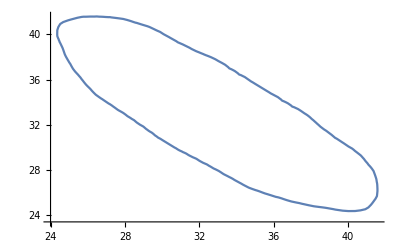

```mathematica
ListLinePlot[mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]],2]]
```

{dphi_2}

====== [dphi_2] 反解校验报告 (容差: 1/100000) ======

概率区间: {0.0387305, 0.961269}

GR 目标区间: {6.24202, 6.44162}

Param 目标区间: {1.98792, 6.35309}

GR下界: 点数=500 | Y>0点数=500 | 平均误差=7.90479×10^-16

GR上界: 点数=500 | Y>0点数=500 | 平均误差=9.11271×10^-16

Param下界: 点数=500 | Y>0点数=500 | 平均误差=2.92613

Param上界: 点数=500 | Y>0点数=500 | 平均误差=2.85993×10^-16

{{10.1,2.10931×10^6},{10.2,2.13019×10^6},{10.3,2.15108×10^6},{10.4,2.17196×10^6},{10.5,2.19284×10^6}}

{{10.1,16.5129},{10.2,16.6764},{10.3,16.8399},{10.4,17.0034},{10.5,17.1669}}

chi1L取值：0.258801

chi2L取值：0.347617

=====================================================

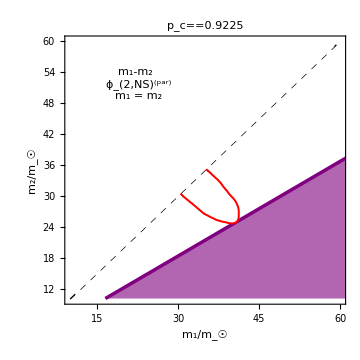

```mathematica
p={"dphi_2"}
probability=prob;
(*probability=0.93;*)
plots[CASE]=PlotMultiInversion[p,{probability},10,60,0.1,cm->True,cd->{1},cu->{1},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiNS},contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]],2]}]
```

```mathematica
(*p={"dphi_2","dphi_4","dphi_5l"}
probability=prob;
probability=0.956;
PlotMultiInversion[p,{probability,0.954, probability},10,60,1,cm->True,cd->{1,1,1},cu->{1,1,1},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiNS,IMRPhenomDPhiNS,IMRPhenomDPhiLNS},contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]],2]}]*)
```

### phi_4

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p={"dphi_4"}; (*换参数改这里*)
CASE="p4";

(*提取 0.005 密度对应的红线*)
contourPD[CASE]={0.001455};
{contourPlotObj[CASE],contourPoints[CASE]}=GetContourPlotAndPoints[m1m2PDF["GR"],m1PriorRange["GR"],m2PriorRange["GR"],contourPD[CASE]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF["GR"],{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{5.44814, 217.926} × {5.44814, 217.926}

等高线值：{0.001455}，共 2 条

第一条前3点：{{30.0511,30.7151},{30.0272,30.7409},{29.8688,30.8727}}

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.93094

可信水平百分比：93.094%

==========================

{dphi_4} 预处理完成，红线包含概率 prob = 0.93094

```mathematica
p="dphi_4"; 
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

{dphi_4}

====== [dphi_4] 反解校验报告 (容差: 1/100000) ======

概率区间: {0.0345302, 0.96547}

GR 目标区间: {43.6686, 46.2435}

Param 目标区间: {-121.589, 45.2369}

GR下界: 点数=300 | Y>0点数=300 | 平均误差=8.28967×10^-16

GR上界: 点数=300 | Y>0点数=300 | 平均误差=1.03976×10^-14

Param下界: 点数=300 | Y>0点数=300 | 平均误差=151.693

Param上界: 点数=300 | Y>0点数=300 | 平均误差=6.6791×10^-15

{{20.1,713611.},{20.2,717161.},{20.3,720707.},{20.4,724261.},{20.5,727809.}}

{{20.1,32.2731},{20.2,32.4337},{20.3,32.5942},{20.4,32.7548},{20.5,32.9153}}

chi1L取值：0.262031

chi2L取值：0.383743

=====================================================

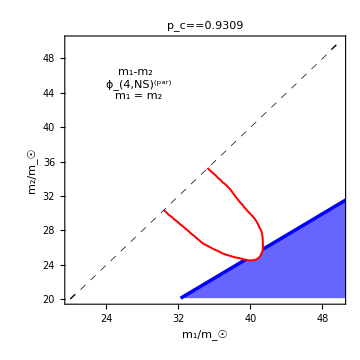

```mathematica
p={"dphi_4"}
probability=prob;
(*probability=0.9309;*)
plots[CASE]=PlotMultiInversion[p,{probability},20,50,0.1,cm->True,cd->{1},cu->{1},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiNS},contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]],2]}]
```

### phi_5l

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p={"dphi_5l"}; (*换参数改这里*)
CASE="p5l";

(*提取 0.005 密度对应的红线*)
contourPD[CASE]={0.000916};
{contourPlotObj[CASE],contourPoints[CASE]}=GetContourPlotAndPoints[m1m2PDF["GR"],m1PriorRange["GR"],m2PriorRange["GR"],contourPD[CASE]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF["GR"],{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{5.44814, 217.926} × {5.44814, 217.926}

等高线值：{0.000916}，共 2 条

第一条前3点：{{35.8291,35.1651},{35.989,35.0458},{36.0486,34.9791}}

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.955895

可信水平百分比：95.5895%

==========================

{dphi_5l} 预处理完成，红线包含概率 prob = 0.955895

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

{dphi_5l}

====== [dphi_5l] 反解校验报告 (容差: 1/100000) ======

概率区间: {0.0220523, 0.977948}

GR 目标区间: {464.757, 467.064}

Param 目标区间: {465.891, 1098.94}

GR下界: 点数=300 | Y>0点数=300 | 平均误差=2.40637×10^-14

GR上界: 点数=300 | Y>0点数=300 | 平均误差=2.88007×10^-14

Param下界: 点数=300 | Y>0点数=300 | 平均误差=5.30539×10^-15

Param上界: 点数=300 | Y>0点数=300 | 平均误差=617.174

{{20.1,34.095},{20.2,34.2646},{20.3,34.4343},{20.4,34.6039},{20.5,34.7735}}

{{20.1,221602.},{20.2,222705.},{20.3,223807.},{20.4,224909.},{20.5,226013.}}

chi1L取值：0.28772

chi2L取值：0.362064

=====================================================

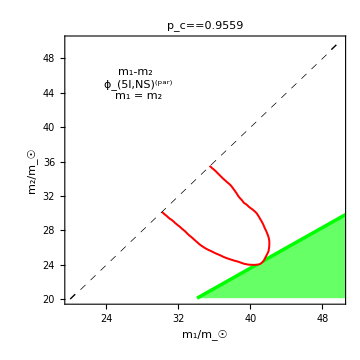

```mathematica
p={"dphi_5l"}
probability=prob;
(*probability=0.955;*)
plots[CASE]=PlotMultiInversion[p,{probability},20,50,0.1,cm->True,cd->{1},cu->{1},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiLNS},contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]],2]}]
```

### phi_6

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p={"dphi_6"}; (*换参数改这里*)
CASE="p6";

(*提取 0.005 密度对应的红线*)
contourPD[CASE]={0.001408};
{contourPlotObj[CASE],contourPoints[CASE]}=GetContourPlotAndPoints[m1m2PDF["GR"],m1PriorRange["GR"],m2PriorRange["GR"],contourPD[CASE]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF["GR"],{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{5.44814, 217.926} × {5.44814, 217.926}

等高线值：{0.001408}，共 2 条

第一条前3点：{{30.0342,30.6982},{29.9905,30.7453},{29.8688,30.8466}}

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.933168

可信水平百分比：93.3168%

==========================

{dphi_6} 预处理完成，红线包含概率 prob = 0.933168

对称边界框：{5.44814, 217.926} × {5.44814, 217.926}

等高线值：{0.001408}，共 2 条

第一条前3点：{{30.0342,30.6982},{29.9905,30.7453},{29.8688,30.8466}}

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.933168

可信水平百分比：93.3168%

==========================

{dphi_6} 预处理完成，红线包含概率 prob = 0.933168

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

{dphi_6}

====== [dphi_6] 反解校验报告 (容差: 1/100000) ======

概率区间: {0.0334161, 0.966584}

GR 目标区间: {-1104.07, -1017.78}

Param 目标区间: {-1053.86, 1453.5}

GR下界: 点数=300 | Y>0点数=300 | 平均误差=1.45519×10^-13

GR上界: 点数=300 | Y>0点数=300 | 平均误差=8.26124×10^-14

Param下界: 点数=300 | Y>0点数=300 | 平均误差=1.43245×10^-13

Param上界: 点数=300 | Y>0点数=300 | 平均误差=1731.77

{{20.1,33.2633},{20.2,33.4288},{20.3,33.5943},{20.4,33.7598},{20.5,33.9253}}

{{20.1,3.83976×10^6},{20.2,3.85886×10^6},{20.3,3.87796×10^6},{20.4,3.89707×10^6},{20.5,3.91617×10^6}}

chi1L取值：0.233562

chi2L取值：0.324994

=====================================================

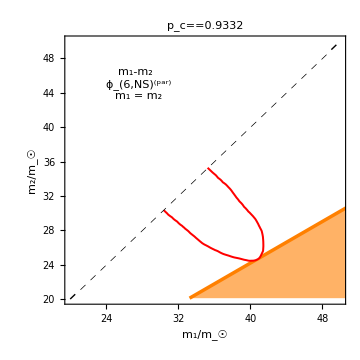

```mathematica
p={"dphi_6"}
probability=prob;
(*probability=0.94;*)
plots[CASE]=PlotMultiInversion[p,{probability},20,50,0.1,cm->True,cd->{1},cu->{1},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiNS},contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]],2]}]
```

### phi_7

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
CASE="p7";

(*提取 0.005 密度对应的红线*)
contourPD[CASE]={0.000916};
{contourPlotObj[CASE],contourPoints[CASE]}=GetContourPlotAndPoints[m1m2PDF["GR"],m1PriorRange["GR"],m2PriorRange["GR"],contourPD[CASE]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF["GR"],{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{5.44814, 217.926} × {5.44814, 217.926}

等高线值：{0.000916}，共 2 条

第一条前3点：{{35.8291,35.1651},{35.989,35.0458},{36.0486,34.9791}}

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.955895

可信水平百分比：95.5895%

==========================

{dphi_6} 预处理完成，红线包含概率 prob = 0.955895

```mathematica
p="dphi_7"; 
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

{dphi_7}

====== [dphi_7] 反解校验报告 (容差: 1/100000) ======

概率区间: {0.02155, 0.97845}

GR 目标区间: {1112.45, 1130.89}

Param 目标区间: {1129.34, 8354.33}

GR下界: 点数=300 | Y>0点数=300 | 平均误差=2.72848×10^-14

GR上界: 点数=300 | Y>0点数=300 | 平均误差=3.71377×10^-14

Param下界: 点数=300 | Y>0点数=300 | 平均误差=1.26571×10^-13

Param上界: 点数=300 | Y>0点数=300 | 平均误差=7223.43

{{20.1,24.5142},{20.2,24.6361},{20.3,24.7581},{20.4,24.8801},{20.5,25.002}}

{{20.1,20.1063},{20.2,20.2076},{20.3,20.3094},{20.4,20.4118},{20.5,20.5146}}

chi1L取值：0.272612

chi2L取值：0.300481

=====================================================

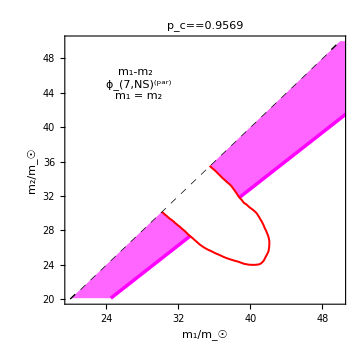

```mathematica
p={"dphi_7"}
probability=prob;
probability=0.9569;
plots[CASE]=PlotMultiInversion[p,{probability},20,50,0.1,cm->True,cd->{1},cu->{1},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiNS},contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]],2]},lineStyles->{{Automatic,Directive[Opacity[0.0]]}}]
```

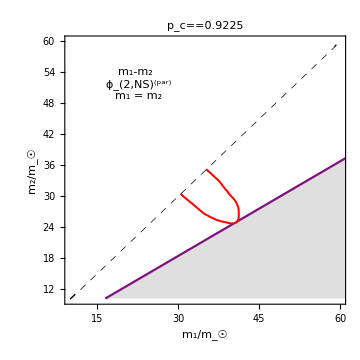
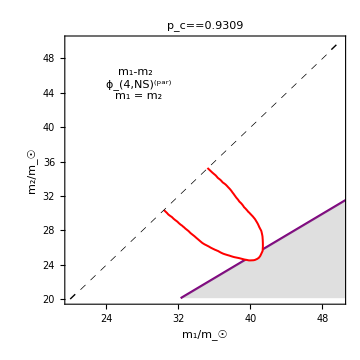
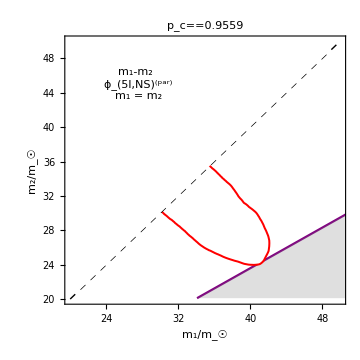
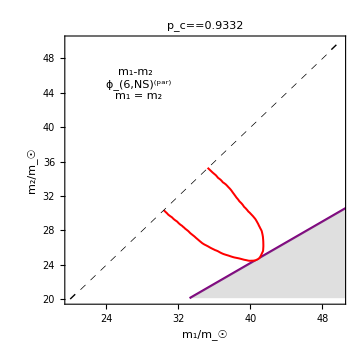
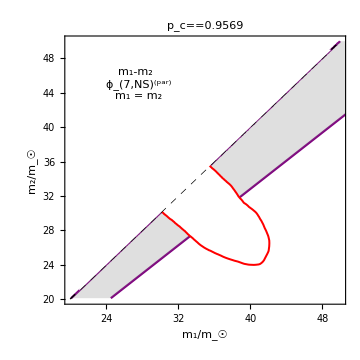
<|p2→-Graphics-,p4→-Graphics-,p5→-Graphics-,p5l→-Graphics-,p6→-Graphics-,p7→-Graphics-|>

```mathematica
plots
```

## 2

### phi_2,4

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
CASE="p24";

(*提取 0.005 密度对应的红线*)
contourPD[CASE]={0.001455};
{contourPlotObj[CASE],contourPoints[CASE]}=GetContourPlotAndPoints[m1m2PDF["GR"],m1PriorRange["GR"],m2PriorRange["GR"],contourPD[CASE]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF["GR"],{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{5.44814, 217.926} × {5.44814, 217.926}

等高线值：{0.001455}，共 2 条

第一条前3点：{{30.0511,30.7151},{30.0272,30.7409},{29.8688,30.8727}}

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.93094

可信水平百分比：93.094%

==========================

{dphi_7} 预处理完成，红线包含概率 prob = 0.93094

{dphi_2,dphi_4}

====== [dphi_2] 反解校验报告 (容差: 1/100000) ======

概率区间: {0.0345302, 0.96547}

GR 目标区间: {6.23648, 6.44165}

Param 目标区间: {1.92581, 6.41195}

GR下界: 点数=300 | Y>0点数=300 | 平均误差=1.43293×10^-15

GR上界: 点数=300 | Y>0点数=300 | 平均误差=8.73375×10^-16

Param下界: 点数=300 | Y>0点数=300 | 平均误差=2.98824

Param上界: 点数=300 | Y>0点数=300 | 平均误差=7.69755×10^-16

{{20.1,4.11049×10^6},{20.2,4.13095×10^6},{20.3,4.15139×10^6},{20.4,4.17183×10^6},{20.5,4.1923×10^6}}

{{20.1,26.6323},{20.2,26.7648},{20.3,26.8973},{20.4,27.0298},{20.5,27.1623}}

chi1L取值：0.258801

chi2L取值：0.347617

=====================================================

====== [dphi_4] 反解校验报告 (容差: 1/100000) ======

概率区间: {0.0345302, 0.96547}

GR 目标区间: {43.6686, 46.2435}

Param 目标区间: {-121.589, 45.2369}

GR下界: 点数=300 | Y>0点数=300 | 平均误差=8.28967×10^-16

GR上界: 点数=300 | Y>0点数=300 | 平均误差=1.03976×10^-14

Param下界: 点数=300 | Y>0点数=300 | 平均误差=151.693

Param上界: 点数=300 | Y>0点数=300 | 平均误差=6.6791×10^-15

{{20.1,713611.},{20.2,717161.},{20.3,720707.},{20.4,724261.},{20.5,727809.}}

{{20.1,32.2731},{20.2,32.4337},{20.3,32.5942},{20.4,32.7548},{20.5,32.9153}}

chi1L取值：0.262031

chi2L取值：0.383743

=====================================================

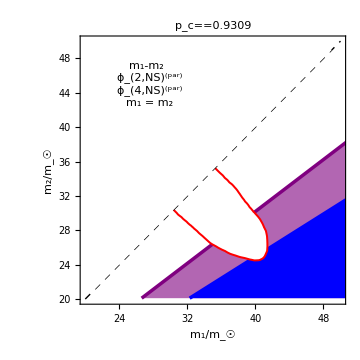

```mathematica
p={"dphi_2","dphi_4"}
probability=prob;
(*probability=0.9309;*)
(*probability=0.9569;*)
plots[CASE]=PlotMultiInversion[p,{probability,probability},20,50,0.1,cm->True,cd->{1,1},cu->{1,1},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiNS,IMRPhenomDPhiNS},contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]],2]},opaqueIndices->{2}]
```

## 3

### phi_2,4,5l

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
CASE="p245l";

(*提取 0.005 密度对应的红线*)
contourPD[CASE]={0.000916};
{contourPlotObj[CASE],contourPoints[CASE]}=GetContourPlotAndPoints[m1m2PDF["GR"],m1PriorRange["GR"],m2PriorRange["GR"],contourPD[CASE]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF["GR"],{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{5.44814, 217.926} × {5.44814, 217.926}

等高线值：{0.000916}，共 2 条

第一条前3点：{{35.8291,35.1651},{35.989,35.0458},{36.0486,34.9791}}

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.955895

可信水平百分比：95.5895%

==========================

{dphi_2,dphi_4} 预处理完成，红线包含概率 prob = 0.955895

{dphi_2,dphi_4,dphi_5l}

====== [dphi_2] 反解校验报告 (容差: 1/100000) ======

概率区间: {0.0220523, 0.977948}

GR 目标区间: {6.21398, 6.44174}

Param 目标区间: {1.70381, 6.61235}

GR下界: 点数=300 | Y>0点数=300 | 平均误差=7.25346×10^-16

GR上界: 点数=300 | Y>0点数=300 | 平均误差=8.79297×10^-16

Param下界: 点数=300 | Y>0点数=300 | 平均误差=3.21025

Param上界: 点数=300 | Y>0点数=300 | 平均误差=0.170549

{{20.1,3.82621×10^6},{20.2,3.84525×10^6},{20.3,3.86429×10^6},{20.4,3.88333×10^6},{20.5,3.90236×10^6}}

{{20.1,20.1},{20.2,20.2},{20.3,20.3},{20.4,20.4},{20.5,20.5}}

chi1L取值：0.258801

chi2L取值：0.347617

=====================================================

====== [dphi_4] 反解校验报告 (容差: 1/100000) ======

概率区间: {0.0220523, 0.977948}

GR 目标区间: {43.4368, 46.245}

Param 目标区间: {-129.266, 54.9643}

GR下界: 点数=300 | Y>0点数=300 | 平均误差=1.00423×10^-14

GR上界: 点数=300 | Y>0点数=300 | 平均误差=5.99224×10^-15

Param下界: 点数=300 | Y>0点数=300 | 平均误差=159.37

Param上界: 点数=300 | Y>0点数=300 | 平均误差=8.71844

{{20.1,679232.},{20.2,682607.},{20.3,685989.},{20.4,689368.},{20.5,692749.}}

{{20.1,20.1},{20.2,20.2},{20.3,20.3001},{20.4,20.3999},{20.5,20.5001}}

chi1L取值：0.262031

chi2L取值：0.383743

=====================================================

====== [dphi_5l] 反解校验报告 (容差: 1/100000) ======

概率区间: {0.0220523, 0.977948}

GR 目标区间: {464.757, 467.064}

Param 目标区间: {465.891, 1098.94}

GR下界: 点数=300 | Y>0点数=300 | 平均误差=2.40637×10^-14

GR上界: 点数=300 | Y>0点数=300 | 平均误差=2.88007×10^-14

Param下界: 点数=300 | Y>0点数=300 | 平均误差=5.30539×10^-15

Param上界: 点数=300 | Y>0点数=300 | 平均误差=617.174

{{20.1,34.095},{20.2,34.2646},{20.3,34.4343},{20.4,34.6039},{20.5,34.7735}}

{{20.1,221602.},{20.2,222705.},{20.3,223807.},{20.4,224909.},{20.5,226013.}}

chi1L取值：0.28772

chi2L取值：0.362064

=====================================================

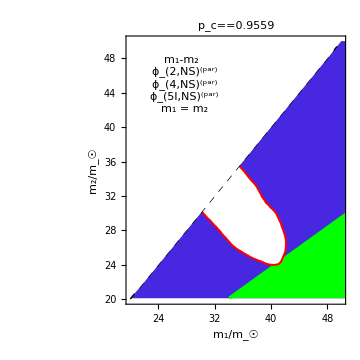

```mathematica
p={"dphi_2","dphi_4","dphi_5l"}
probability=prob;
(*probability=0.9309;*)
plots[CASE]=PlotMultiInversion[p,{probability,probability,probability},20,50,0.1,cm->True,cd->{1,1,1},cu->{1,1,1},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiNS,IMRPhenomDPhiNS,IMRPhenomDPhiLNS},contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]],2]},lineStyles->{Directive[Opacity[0.0]],Directive[Opacity[0.0]],Automatic},opaqueIndices->{3}]
```

## 4

### phi_2,4,5l,6

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
CASE="p245l6";

(*提取 0.005 密度对应的红线*)
contourPD[CASE]={0.000916};
{contourPlotObj[CASE],contourPoints[CASE]}=GetContourPlotAndPoints[m1m2PDF["GR"],m1PriorRange["GR"],m2PriorRange["GR"],contourPD[CASE]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF["GR"],{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{5.44814, 217.926} × {5.44814, 217.926}

等高线值：{0.000916}，共 2 条

第一条前3点：{{35.8291,35.1651},{35.989,35.0458},{36.0486,34.9791}}

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.955895

可信水平百分比：95.5895%

==========================

{dphi_7} 预处理完成，红线包含概率 prob = 0.955895

{dphi_2,dphi_4,dphi_5l,dphi_6}

====== [dphi_2] 反解校验报告 (容差: 1/100000) ======

概率区间: {0.0220523, 0.977948}

GR 目标区间: {6.21398, 6.44174}

Param 目标区间: {1.70381, 6.61235}

GR下界: 点数=300 | Y>0点数=300 | 平均误差=7.25346×10^-16

GR上界: 点数=300 | Y>0点数=300 | 平均误差=8.79297×10^-16

Param下界: 点数=300 | Y>0点数=300 | 平均误差=3.21025

Param上界: 点数=300 | Y>0点数=300 | 平均误差=0.170549

{{20.1,3.82621×10^6},{20.2,3.84525×10^6},{20.3,3.86429×10^6},{20.4,3.88333×10^6},{20.5,3.90236×10^6}}

{{20.1,20.1},{20.2,20.2},{20.3,20.3},{20.4,20.4},{20.5,20.5}}

chi1L取值：0.258801

chi2L取值：0.347617

=====================================================

====== [dphi_4] 反解校验报告 (容差: 1/100000) ======

概率区间: {0.0220523, 0.977948}

GR 目标区间: {43.4368, 46.245}

Param 目标区间: {-129.266, 54.9643}

GR下界: 点数=300 | Y>0点数=300 | 平均误差=1.00423×10^-14

GR上界: 点数=300 | Y>0点数=300 | 平均误差=5.99224×10^-15

Param下界: 点数=300 | Y>0点数=300 | 平均误差=159.37

Param上界: 点数=300 | Y>0点数=300 | 平均误差=8.71844

{{20.1,679232.},{20.2,682607.},{20.3,685989.},{20.4,689368.},{20.5,692749.}}

{{20.1,20.1},{20.2,20.2},{20.3,20.3001},{20.4,20.3999},{20.5,20.5001}}

chi1L取值：0.262031

chi2L取值：0.383743

=====================================================

====== [dphi_5l] 反解校验报告 (容差: 1/100000) ======

概率区间: {0.0220523, 0.977948}

GR 目标区间: {464.757, 467.064}

Param 目标区间: {465.891, 1098.94}

GR下界: 点数=300 | Y>0点数=300 | 平均误差=2.40637×10^-14

GR上界: 点数=300 | Y>0点数=300 | 平均误差=2.88007×10^-14

Param下界: 点数=300 | Y>0点数=300 | 平均误差=5.30539×10^-15

Param上界: 点数=300 | Y>0点数=300 | 平均误差=617.174

{{20.1,34.095},{20.2,34.2646},{20.3,34.4343},{20.4,34.6039},{20.5,34.7735}}

{{20.1,221602.},{20.2,222705.},{20.3,223807.},{20.4,224909.},{20.5,226013.}}

chi1L取值：0.28772

chi2L取值：0.362064

=====================================================

====== [dphi_6] 反解校验报告 (容差: 1/100000) ======

概率区间: {0.0220523, 0.977948}

GR 目标区间: {-1104.1, -1008.69}

Param 目标区间: {-1176.35, 1586.91}

GR下界: 点数=300 | Y>0点数=300 | 平均误差=1.43245×10^-13

GR上界: 点数=300 | Y>0点数=300 | 平均误差=9.62549×10^-14

Param下界: 点数=300 | Y>0点数=300 | 平均误差=72.2229

Param上界: 点数=300 | Y>0点数=300 | 平均误差=1865.18

{{20.1,20.1},{20.2,20.2},{20.3,20.3},{20.4,20.4},{20.5,20.5}}

{{20.1,3.56511×10^6},{20.2,3.58285×10^6},{20.3,3.60059×10^6},{20.4,3.61832×10^6},{20.5,3.63606×10^6}}

chi1L取值：0.233562

chi2L取值：0.324994

=====================================================

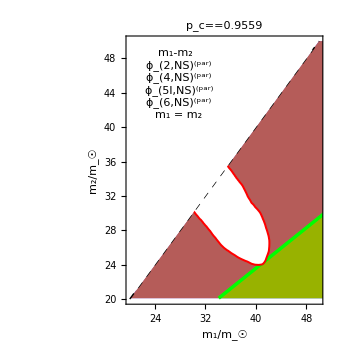

```mathematica
p={"dphi_2","dphi_4","dphi_5l","dphi_6"}
probability=prob;
(*probability=0.9309;*)
plots[CASE]=PlotMultiInversion[p,{probability,probability,probability,probability},20,50,0.1,cm->True,cd->{1,1,1,1},cu->{1,1,1,1},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiNS,IMRPhenomDPhiNS,IMRPhenomDPhiLNS,IMRPhenomDPhiNS},contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]],2]},lineStyles->{Directive[Opacity[0.0]],Directive[Opacity[0.0]],Automatic,Directive[Opacity[0.0]]},opaqueIndices->{3}]
```

## 5

### phi_2,4,5l,6,7

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
CASE="p245l67";

(*提取 0.005 密度对应的红线*)
contourPD[CASE]={0.000916};
{contourPlotObj[CASE],contourPoints[CASE]}=GetContourPlotAndPoints[m1m2PDF["GR"],m1PriorRange["GR"],m2PriorRange["GR"],contourPD[CASE]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF["GR"],{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{5.44814, 217.926} × {5.44814, 217.926}

等高线值：{0.000916}，共 2 条

第一条前3点：{{35.8291,35.1651},{35.989,35.0458},{36.0486,34.9791}}

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.955895

可信水平百分比：95.5895%

==========================

{dphi_2,dphi_4,dphi_5l,dphi_6,dphi_7} 预处理完成，红线包含概率 prob = 0.955895

{dphi_2,dphi_4,dphi_5l,dphi_6,dphi_7}

====== [dphi_2] 反解校验报告 (容差: 1/100000) ======

概率区间: {0.02155, 0.97845}

GR 目标区间: {6.21326, 6.44174}

Param 目标区间: {1.69442, 6.62338}

GR下界: 点数=300 | Y>0点数=300 | 平均误差=4.52971×10^-16

GR上界: 点数=300 | Y>0点数=300 | 平均误差=2.10202×10^-16

Param下界: 点数=300 | Y>0点数=300 | 平均误差=3.21963

Param上界: 点数=300 | Y>0点数=300 | 平均误差=0.181585

{{20.1,3.81504×10^6},{20.2,3.83403×10^6},{20.3,3.85302×10^6},{20.4,3.87198×10^6},{20.5,3.89098×10^6}}

{{20.1,20.1},{20.2,20.2},{20.3,20.3},{20.4,20.4},{20.5,20.5}}

chi1L取值：0.258801

chi2L取值：0.347617

=====================================================

====== [dphi_4] 反解校验报告 (容差: 1/100000) ======

概率区间: {0.02205, 0.97795}

GR 目标区间: {43.4368, 46.245}

Param 目标区间: {-129.266, 54.9643}

GR下界: 点数=300 | Y>0点数=300 | 平均误差=1.00423×10^-14

GR上界: 点数=300 | Y>0点数=300 | 平均误差=5.99224×10^-15

Param下界: 点数=300 | Y>0点数=300 | 平均误差=159.37

Param上界: 点数=300 | Y>0点数=300 | 平均误差=8.71844

{{20.1,679232.},{20.2,682607.},{20.3,685989.},{20.4,689368.},{20.5,692749.}}

{{20.1,20.1},{20.2,20.2},{20.3,20.3001},{20.4,20.3999},{20.5,20.5001}}

chi1L取值：0.262031

chi2L取值：0.383743

=====================================================

====== [dphi_5l] 反解校验报告 (容差: 1/100000) ======

概率区间: {0.02155, 0.97845}

GR 目标区间: {464.757, 467.076}

Param 目标区间: {464.453, 1100.21}

GR下界: 点数=300 | Y>0点数=300 | 平均误差=5.68434×10^-14

GR上界: 点数=300 | Y>0点数=300 | 平均误差=2.55795×10^-14

Param下界: 点数=300 | Y>0点数=300 | 平均误差=0.303217

Param上界: 点数=300 | Y>0点数=300 | 平均误差=618.446

{{20.1,20.1},{20.2,20.2},{20.3,20.3},{20.4,20.4},{20.5,20.5}}

{{20.1,221147.},{20.2,222248.},{20.3,223348.},{20.4,224448.},{20.5,225549.}}

chi1L取值：0.28772

chi2L取值：0.362064

=====================================================

====== [dphi_6] 反解校验报告 (容差: 1/100000) ======

概率区间: {0.02155, 0.97845}

GR 目标区间: {-1104.1, -1008.23}

Param 目标区间: {-1183.96, 1596.95}

GR下界: 点数=300 | Y>0点数=300 | 平均误差=1.44003×10^-13

GR上界: 点数=300 | Y>0点数=300 | 平均误差=9.54969×10^-14

Param下界: 点数=300 | Y>0点数=300 | 平均误差=79.8361

Param上界: 点数=300 | Y>0点数=300 | 平均误差=1875.22

{{20.1,20.1},{20.2,20.2},{20.3,20.3},{20.4,20.4},{20.5,20.5}}

{{20.1,3.54603×10^6},{20.2,3.56367×10^6},{20.3,3.58131×10^6},{20.4,3.59895×10^6},{20.5,3.6166×10^6}}

chi1L取值：0.233562

chi2L取值：0.324994

=====================================================

====== [dphi_7] 反解校验报告 (容差: 1/100000) ======

概率区间: {0.02155, 0.97845}

GR 目标区间: {1112.45, 1130.89}

Param 目标区间: {1129.34, 8354.33}

GR下界: 点数=300 | Y>0点数=300 | 平均误差=2.72848×10^-14

GR上界: 点数=300 | Y>0点数=300 | 平均误差=3.71377×10^-14

Param下界: 点数=300 | Y>0点数=300 | 平均误差=1.26571×10^-13

Param上界: 点数=300 | Y>0点数=300 | 平均误差=7223.43

{{20.1,24.5142},{20.2,24.6361},{20.3,24.7581},{20.4,24.8801},{20.5,25.002}}

{{20.1,20.1063},{20.2,20.2076},{20.3,20.3094},{20.4,20.4118},{20.5,20.5146}}

chi1L取值：0.272612

chi2L取值：0.300481

=====================================================

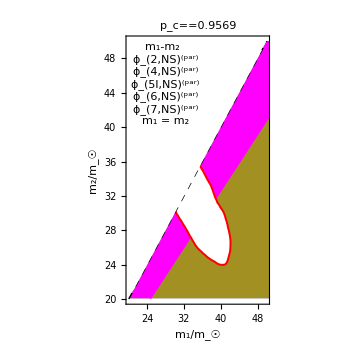

```mathematica
p={"dphi_2","dphi_4","dphi_5l","dphi_6","dphi_7"}
probability=prob;
probability=0.9569;
plots[CASE]=PlotMultiInversion[p,{probability,0.9559,probability,probability,probability},20,50,0.1,cm->True,cd->{1,1,1,1,1},cu->{1,1,1,1,1},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiNS,IMRPhenomDPhiNS,IMRPhenomDPhiLNS,IMRPhenomDPhiNS,IMRPhenomDPhiNS},contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]],2]},lineStyles->{Directive[Opacity[0.0]],Directive[Opacity[0.0]],Directive[Opacity[0.0]],Directive[Opacity[0.0]],{Automatic,Directive[Opacity[0.0]]}},opaqueIndices->{5}]
```

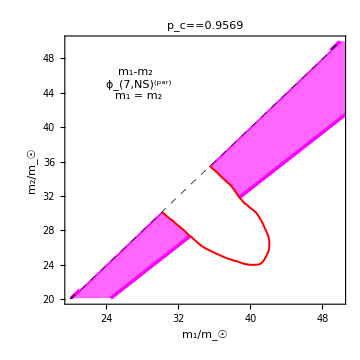
<|p245l67→-Graphics-,p4→-Graphics-,p2→-Graphics-,p5l→-Graphics-,p6→-Graphics-,p7→-Graphics-,p24→-Graphics-,p245l→-Graphics-,p245l6→-Graphics-|>

```mathematica
plots
```

# Total plots

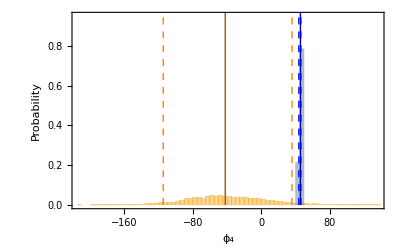

正在导出矢量图: plot_dphi_4_comp.pdf ...

正在导出矢量图: plot_dphi_7_comp.pdf ...

```mathematica
p="dphi_4"; 
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],Style["4",Italic]
,50
,Automatic
]
p="dphi_7"; 
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],Style["7",Italic]
,50
,Automatic
];
(*1. 定义你要存放 PDF 的文件夹名称*)
targetDir=FileNameJoin[{"D:\\Documents\\workspace\\课题\\论文\\fig\\","comp"}];

(*2. 如果目录不存在，则自动创建*)
If[!DirectoryQ[targetDir],CreateDirectory[targetDir];
Print["已自动创建目录: ",targetDir]];

Do[Print["正在导出矢量图: plot_",key,"_comp.pdf ..."];
Export[FileNameJoin[{targetDir,eventID<>"_"<>key<>"_comp.pdf"}],compPlots[key],"PDF",AllowRasterization->False (*强制全矢量输出，绝对高清*),ImageSize->500],
{key,Keys[compPlots]}]
```

```mathematica
(*1. 定义你要存放 PDF 的文件夹名称*)
targetDir=FileNameJoin[{"D:\\Documents\\workspace\\课题\\论文\\fig\\",eventID}];

(*2. 如果目录不存在，则自动创建*)
If[!DirectoryQ[targetDir],CreateDirectory[targetDir];
Print["已自动创建目录: ",targetDir]];

Do[Print["正在导出矢量图: plot_",key,".pdf ..."];
Export[FileNameJoin[{targetDir,eventID<>"_"<>key<>".pdf"}],plots[key],"PDF",AllowRasterization->False (*强制全矢量输出，绝对高清*),ImageSize->500],
{key,Keys[plots]}]
```

正在导出矢量图: plot_dphi_5l.pdf ...

正在导出矢量图: plot_dphi_6.pdf ...

正在导出矢量图: plot_dphi_7.pdf ...

正在导出矢量图: plot_dalpha_2.pdf ...

正在导出矢量图: plot_dalpha_3.pdf ...

正在导出矢量图: plot_dalpha_4.pdf ...